## Demo for the options

```mathematica
M2TeXToString[tasfasdfsdafest]
M2TeXToString[3242434]
M2TeXToString[{asdfasdf}]
```

tasfasdfsdafest

3242434

{asdfasdf}

```mathematica
test=M2TeXSetCommand["usepackage"];
M2TeXToString[test]
```

M2TeXSetCommand[usepackage]

```mathematica
test=M2TeXSetCommand[
"usepackage",
"Parameter"->{1,2,3,4},
"OptionalParameter"->{1,2,3}
];
M2TeXToString[test]
```

M2TeXSetCommand[usepackage, Parameter -> {1, 2, 3, 4}, OptionalParameter -> {1, 2, 3}]

```mathematica
test=M2TeXSetPackage[
"Parameter"->{1,2,3,4}
];
M2TeXToString[test]
```

M2TeXSetPackage[Parameter -> {1, 2, 3, 4}]

```mathematica
M2TeXSetOptionalOption[{1,2,3,4}];
M2TeXToString[%]
```

M2TeXSetOptionalOption[{1, 2, 3, 4}]

```mathematica
test=M2TeXSetPackage[
"ParameterList"->{
M2TeXSetOption[asfasf],
M2TeXSetOptionalOption[{1,2,3,4}]
}
];
M2TeXToString[test]
```

M2TeXSetPackage[ParameterList -> {M2TeXSetOption[asfasf], M2TeXSetOptionalOption[{1, 2, 3, 4}]}]

```mathematica
test=M2TeXSetEnvironment[
"document",
"ParameterList"->{
M2TeXSetOption[asfasf],
M2TeXSetOptionalOption[{1,2,3,4}]
}
];
M2TeXToString[test]
```

M2TeXSetEnvironment[document, ParameterList -> {M2TeXSetOption[asfasf], M2TeXSetOptionalOption[{1, 2, 3, 4}]}]

```mathematica
AppendTo
```

AppendTo

```mathematica
abc=f[{1,2,3}]
```

f[{1,2,3}]

```mathematica
AppendTo[abc⟦1⟧,5]
```

{1,2,3,5}

```mathematica
abc
```

f[{1,2,3,5}]

```mathematica
M2TeXSetDocument[]
M2TeXToString[%]
```

M2TeXSetDocument[]

M2TeXSetDocument[]

```mathematica
M2TeXDocumentToString[]
```

M2TeXDocumentToString[]

```mathematica
M2TeXAppendToDocument[2]
M2TeXAppendToDocument[2]
M2TeXAppendToDocument[2]
M2TeXAppendToDocument[2]
```

M2TeXAppendToDocument[2]

M2TeXAppendToDocument[2]

M2TeXAppendToDocument[2]

«1 more identical outputs»

```mathematica
M2TeXAppendToDocument[test]
```

M2TeXAppendToDocument[M2TeXSetEnvironment[document,ParameterList→{M2TeXSetOption[asfasf],M2TeXSetOptionalOption[{1,2,3,4}]}]]

```mathematica
SetDirectory[NotebookDirectory[]];
M2TeXSetDocument["tikz"]
M2TeXAppendToDocument["asdfasdf"]
M2TeXAppendToDocument["2asdfasdf"]
M2TeXDocumentToString[]
```

M2TeXSetDocument[tikz]

M2TeXAppendToDocument[asdfasdf]

M2TeXAppendToDocument[2asdfasdf]

M2TeXDocumentToString[]

```mathematica
(*M2TeXGeneratePdf["test"]*)
```

## LATEX Plots

```mathematica
<<M2TeX`
SetDirectory[NotebookDirectory[]];
```

Set the default document values

```mathematica
width=5;
defaultM2TexPlotOptions={"width="<>ToString[N[width],CForm]<>"cm","height="<>ToString[N[width/GoldenRatio],CForm]<>"cm","scale only axis"}
```

{width=5.cm,height=3.090169943749474cm,scale only axis}

Add the document and tikz environment

```mathematica
M2TeXSetDocument["tikz"]
M2TeXAppendToDocument[M2TeXSetEnvironment["tikzpicture"]]
```

Add the axis

```mathematica
M2TeXAppendToDocument[M2TeXSetEnvironment[
"axis",
"ParameterList"->{
M2TeXSetOptionalOption[{
defaultM2TexPlotOptions,
"ymin=-2"
}]
}
]]
```

Add the plot

```mathematica
table=Table[{x,Sin[5x]},{x,0,2π,2π/1000.1}];
M2TeXAppendToDocument[M2TeXSetPlot[table,"red,thick"]];

table=Table[{x,Cos[2x]},{x,0,2π,2π/1000.1}];
M2TeXAppendToDocument[M2TeXSetPlot[table,"blue,thick"]];

table=Table[{x,Log[x]},{x,0.00001,2π,2π/1000.1}];
M2TeXAppendToDocument[M2TeXSetPlot[table,"green,thick"]];
```

Generate the pdf

```mathematica
plot=M2TeXGeneratePdf["plot"];
Show[plot,ImageSize->500]
```

DeleteFile::fdnfnd: Directory or file plot.bbl not found.

-Graphics-

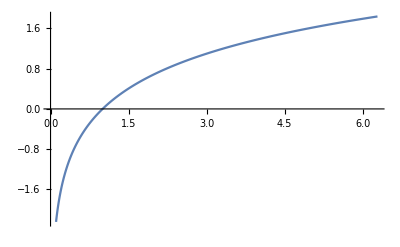

```mathematica
ListLinePlot[table]
```

```mathematica
M2TeXToString[M2TeXSetCommand["usepackage","Parameter"->{"asdf",asdf2,adsf,{asdf}}]]
```

\usepackage{asdf, asdf2, adsf, asdf}

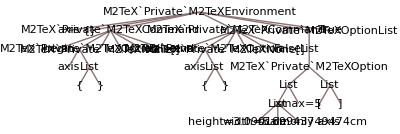

-Graphics-

```mathematica
M2TeXSetEnvironment[
"axis",
"ParameterList"->{
M2TeXSetOptionalOption[{
defaultM2TexPlotOptions,
"xmax=5"
}]
}
]//TreeForm
```

## PlotFunction

```mathematica
plotPDF[table_]:=Module[{},
M2TeXSetDocument["tikz"];
M2TeXAppendToDocument[M2TeXSetEnvironment["tikzpicture"]];
M2TeXAppendToDocument[M2TeXSetEnvironment[
"axis",
"ParameterList"->{
M2TeXSetOptionalOption[defaultM2TexPlotOptions]
}
]];
M2TeXAppendToDocument[M2TeXSetPlot[table,"black,thick"]];
M2TeXGeneratePdf["plot"]⟦1⟧
];
```

# MAtex stuff

```mathematica
(*True if file exists and is not a directory*)
fileQ[file_]:=FileType[file]===File
```

```mathematica
path=Quiet@Check[AbsoluteFileName@First@ReadList["!where pdflatex.exe",String,1],None]
```

```mathematica
dirpath=NotebookDirectory[]
```

```mathematica
$environment=Association@GetEnvironment[]
```

```mathematica
RunProcess[{path,"-halt-on-error","-interaction=nonstopmode","plot.tex"},ProcessDirectory->dirpath,ProcessEnvironment->$environment]
```

```mathematica
"\""
```

"

# Demo

## Options

Full definition

```mathematica
M2TeXOption["value","OpenCloseCharacter"->{"<Open>","<Close>"}];
%//M2TeXToString
```

<Open>value<Close>

Default for options also works with list of options

```mathematica
M2TeXOption["value"];
%//M2TeXToString
M2TeXOption[{"value",{"op2",{"op3","op4"}}}];
%//M2TeXToString
```

{value}

{value, op2, op3, op4}

Optional options

```mathematica
M2TeXOptionOptional[{"optional1","optional2"}];
%//M2TeXToString
```

[optional1, optional2]

## Commands

Full definition

```mathematica
M2TeXCommand[
"dostuff",
"Parameter"->"val1",
"ParameterOptional"->"val2",
"ParameterList"->None,
"StartCharacter"->"<\\>",
"EndCharacter"->"</>"
];
%//M2TeXToString
```

<\>dostuff[val2]{val1}</>

With parameter list, the type of options can be given by the user

```mathematica
M2TeXCommand[
"dostuff",
"ParameterList"->{
M2TeXOption[{"op1","op11"}],
M2TeXOptionOptional[{"op2","op22"}],
M2TeXOption["op3"]
}
];
%//M2TeXToString
```

\dostuff{op1, op11}[op2, op22]{op3}

Typical behavioud

```mathematica
M2TeXCommand["dostuff"];
%//M2TeXToString
M2TeXCommand["dostuff","opt"];
%//M2TeXToString
M2TeXCommand["dostuff",{"opt","OPT"},"opt2"];
%//M2TeXToString
M2TeXCommand["dostuff",,"opt2"];
%//M2TeXToString
```

\dostuff

\dostuff{opt}

\dostuff[opt2]{opt, OPT}

\dostuff[opt2]

Packages

```mathematica
M2TeXPackage["name",{"opt1","opt2"}];
%//M2TeXToString
```

\usepackage[opt1, opt2]{name}

## Environments

Full definition

```mathematica
M2TeXEnvironment[
"document",
"ParameterList"->{
M2TeXOption["op1"],
M2TeXOptionOptional["op2"]
},
"StartCommand"->"START",
"EndCommand"->"END"
];
%//M2TeXToString
```

START{op1}[op2]
END

Short definitions

```mathematica
M2TeXEnvironment["document"];
%//M2TeXToString
M2TeXEnvironment["document",{
M2TeXOption["op1"],
M2TeXOptionOptional["op2"]
}];
%//M2TeXToString
```

\begin{document}
\end{document}

\begin{document}{op1}[op2]
\end{document}

Add content to environment

```mathematica
doc=M2TeXEnvironment["document"];
M2TeXAddToEnvironment[doc,M2TeXCommand["section","Introduction"]]
M2TeXAddToEnvironment[doc,"Bla bla bla..."]
doc//M2TeXToString
```

\begin{document}
\section{Introduction}
Bla bla bla...
\end{document}

When an environment is added the next items are added inside that environment

```mathematica
doc=M2TeXEnvironment["document"];
M2TeXAddToEnvironment[doc,M2TeXEnvironment["picture"]]
M2TeXAddToEnvironment[doc,"Bla bla bla..."]
doc//M2TeXToString
```

\begin{document}
\begin{picture}
Bla bla bla...
\end{picture}
\end{document}

The M2TeXCloseActiveEnvironment command closes the active environment and returns to the previous one

```mathematica
doc=M2TeXEnvironment["document"];
M2TeXAddToEnvironment[doc,M2TeXEnvironment["picture"]]
M2TeXAddToEnvironment[doc,"picture"]
M2TeXCloseActiveEnvironment[doc]
M2TeXAddToEnvironment[doc,"Bla bla bla..."]
doc//M2TeXToString
```

\begin{document}
\begin{picture}
picture
\end{picture}
Bla bla bla...
\end{document}

The main environment can not be closed

```mathematica
doc=M2TeXEnvironment["document"];
M2TeXAddToEnvironment[doc,M2TeXEnvironment["picture"]]
M2TeXAddToEnvironment[doc,"Text1"]
M2TeXCloseActiveEnvironment[doc]
M2TeXAddToEnvironment[doc,"Text2"]
M2TeXCloseActiveEnvironment[doc]
M2TeXAddToEnvironment[doc,"Text3"]
doc//M2TeXToString
```

Error, depth not long enough!

\begin{document}
\begin{picture}
Text1
\end{picture}
Text2
Text3
\end{document}

## Document templates

Following templates are available

```mathematica
M2TeXTemplates["article"];
%//M2TeXToString
```

\documentclass{scrartcl}

\usepackage[T1]{fontenc}
\usepackage[utf8]{inputenc}
\usepackage{amsmath}

\begin{document}
\end{document}

```mathematica
M2TeXTemplates["tikz"];
%//M2TeXToString
```

\documentclass[class=scrartcl]{standalone}

\usepackage[T1]{fontenc}
\usepackage[utf8]{inputenc}
\usepackage{amsmath}
\usepackage{tikz}
\usepackage{pgfplots}
\pgfplotsset{compat=newest,tick label style={font=\footnotesize}}

\begin{document}
\end{document}

Documents behave the same way as environments

```mathematica
doc=M2TeXTemplates["standalone"];
M2TeXAddToEnvironment[doc,"stuff in document"]
doc//M2TeXToString
```

\documentclass[class=scrartcl]{standalone}

\usepackage[T1]{fontenc}
\usepackage[utf8]{inputenc}
\usepackage{amsmath}
\usepackage{tikz}
\usepackage{pgfplots}
\pgfplotsset{compat=newest,tick label style={font=\footnotesize}}

\begin{document}
stuff in document
\end{document}

## TikZ tools

Command for TikZ

```mathematica
M2TeXTikZCommand["node"];
%//M2TeXToString
M2TeXTikZCommand["node","at (0,0)"];
%//M2TeXToString
M2TeXTikZCommand["node","at (0,0)","black"];
%//M2TeXToString
M2TeXTikZCommand["node",,"black"];
%//M2TeXToString
```

\node;

\node at (0,0);

\node[black] at (0,0);

\node[black];

Axis for Pgf Plots

```mathematica
M2TeXTikZAxis["meins"];
%//M2TeXToString
```

\begin{axis}[meins]
\end{axis}

2D Plot from datapoints

```mathematica
M2TeXTikZPlot[{{1,3},{2,4}},{black,white}];
%//M2TeXToString
```

\addplot[black, white] coordinates{%
(1, 3)%
(2, 4)%
};

2D Plot from datapoints, with non numeric values

```mathematica
M2TeXTikZPlot[{{1,3},{a,4}},{black,white}];
%//M2TeXToString
```

Non numeric value!

\addplot[black, white] coordinates{%
(1, 3)%
};

## Global document structure

A global document or environment can be set to simplify the commands

```mathematica
M2TeXSetGlobal[M2TeXEnvironment["doc"]]
M2TeXToStringGlobal[]
```

\begin{doc}
\end{doc}

Now the items are added to the global item if no parent item is given

```mathematica
M2TeXAddToEnvironment["text"]
M2TeXToStringGlobal[]
```

\begin{doc}
text
\end{doc}

If a string is given, a template will be set

```mathematica
M2TeXSetGlobal["article"]
M2TeXToStringGlobal[]
```

\documentclass{scrartcl}

\usepackage[T1]{fontenc}
\usepackage[utf8]{inputenc}
\usepackage{amsmath}

\begin{document}
\end{document}

## Compile in LaTeX

Set the current directory

```mathematica
SetDirectory[NotebookDirectory[]];
```

Generate a minimal example

```mathematica
doc=M2TeXTemplates["article"];
M2TeXAddToEnvironment[doc,M2TeXCommand["Huge"]]
M2TeXAddToEnvironment[doc,"Page 1"]
M2TeXAddToEnvironment[doc,"\\newpage"]
M2TeXAddToEnvironment[doc,"Page 2"]
M2TeXToString[doc]
```

\documentclass{scrartcl}

\usepackage[T1]{fontenc}
\usepackage[utf8]{inputenc}
\usepackage{amsmath}

\begin{document}
\Huge
Page 1
\newpage
Page 2
\end{document}

Execute the example, the output is the log string as well as the images

```mathematica
out=M2TeXGeneratePDF["test",doc];
out[[1]]
```

{-Graphics-,-Graphics-}

This option also copies the tex file to the working directory

```mathematica
M2TeXGeneratePDF["test",doc,"SaveTeX"->True];
```

This option imports the pdf file and not a png copy

```mathematica
out=M2TeXGeneratePDF["test",doc,"OutputPDF"->True];
out[[1]]
```

{-Graphics-,-Graphics-}